```mathematica
(* TEST *)
Neff = 10000;
 (* time in generations *)
tfin = 5000;
expcoeff=3;
n=18;
(* time in 2Neff generations *)
tfinC = tfin / (2*Neff);
selcoeff=4;
Clear[resultmat]
blah=NDSolve[{D[g[x,t],t] == -γ*x*(1-x)*D[g[x,t],x]+1/(2*ρ)*x*(1-x)*D[g[x,t],{x,2}],g[x,0]==θ*Exp[2*γ]*(1-Exp[-2*γ*(1-x)])/(Exp[2*γ]-1),g[0,t]==θ*ρ,g[1,t]==0}/.{γ->(2*Neff*(-10^(-selcoeff))),θ->1,ρ->Exp[expcoeff*t]},g,{x,0,1},{t,0,tfinC},MaxStepSize->.00025];
sampleFreqSpec = Table[Binomial[n,i]*NIntegrate[Evaluate[g[x,tfinC]/(x*(1-x))*x^i*(1-x)^(n-i)/.blah],{x,0,1}],{i,1,(n-1)}];
resultmat = Flatten[sampleFreqSpec/Total[sampleFreqSpec][[1]]];
ListPlot[resultmat,PlotRange -> {{1,18},{0,1}}]
Print[resultmat]
```

```mathematica
(*neutral model*)
(*constant-size*)
Clear[selmathum]
Do[Neff = 10000;
n=18;
tfinC = tfin / (2*Neff);
blah = NDSolve[{D[g[x,t],t] == -γ*x*(1-x)*D[g[x,t],x]+1/(2*ρ)*x*(1-x)*D[g[x,t],{x,2}],g[x,0]==θ*(1-x),g[0,t]==θ*ρ,g[1,t]==0}/.{γ->0,θ->1,ρ->1},g,{x,0,1},{t,0,tfinC},MaxStepSize->.0005];
Print["neutral"," ","constant"," ",tfin];
sampleFreqSpec = Table[Binomial[n,i]*NIntegrate[Evaluate[g[x,tfinC]/(x*(1-x))*x^i*(1-x)^(n-i)/.blah],{x,0,1}],{i,1,(n-1)}];
(*resultmat= Table[Evaluate[g[x,tfinC]/(x)/.x->i/100/.blah],{i,1,99}];*)
resultmat = Flatten[sampleFreqSpec];
selmathum[0][tfin]["const"]=resultmat[[All]];
Export[StringJoin[{{"selmathum/selmathum_"},ToString[0],{"_t"},ToString[tfin],{"_exp0.txt"}}],selmathum[0][tfin]["const"]]
,{tfin,{1000}}]
```

```mathematica
(*neutral model*)
(*exponentially growing population, t=13000, r=1*)
Clear[selmathum]
Do[ 
Do[
n=18;
Neff =10000;
tfinC = tfin / (2*Neff);
blah =NDSolve[{D[g[x,t],t] == -γ*x*(1-x)*D[g[x,t],x]+1/(2*ρ)*x*(1-x)*D[g[x,t],{x,2}],g[x,0]==θ*(1-x),g[0,t]==θ*ρ,g[1,t]==0}/.{γ->0,θ->1,ρ->Exp[expcoeff*t]},g,{x,0,1},{t,0,tfinC},MaxStepSize->.0005];
Print["neutral"," ",expcoeff," ",tfin];
sampleFreqSpec = Table[Binomial[n,i]*NIntegrate[Evaluate[g[x,tfinC]/(x*(1-x))*x^i*(1-x)^(n-i)/.blah],{x,0,1}],{i,1,(n-1)}];
resultmat = Flatten[sampleFreqSpec];
selmathum[0][tfin][expcoeff]=resultmat[[All]];
Export[StringJoin[{{"selmathum/selmathum_"},ToString[0],{"_t"},ToString[tfin],{"_exp"},ToString[expcoeff],{".txt"}}],selmathum[0][tfin][expcoeff]],{tfin,{13000}}],{expcoeff,{1}}]
```

```mathematica
(* selection model *)
(* constant-size *)
Clear[selmathum]
Do[
Do[
n=18;
Neff =10000;
tfinC = tfin / (2*Neff);
blah =NDSolve[{D[g[x,t],t] == -γ*x*(1-x)*D[g[x,t],x]+1/(2*ρ)*x*(1-x)*D[g[x,t],{x,2}],g[x,0]==θ*Exp[2*γ]*(1-Exp[-2*γ*(1-x)])/(Exp[2*γ]-1),g[0,t]==θ*ρ,g[1,t]==0}/.{γ->(2*Neff*(-10^(-selcoeff))),θ->1,ρ->1},g,{x,0,1},{t,0,tfinC},MaxStepSize->.0005];
Print[selcoeff," constant ",tfin];
sampleFreqSpec = Table[Binomial[n,i]*NIntegrate[Evaluate[g[x,tfinC]/x*x^i*(1-x)^(n-i)/.blah],{x,0,1}],{i,1,(n-1)}];
resultmat = Flatten[sampleFreqSpec];
selmathum[selcoeff][tfin]["const"]=resultmat[[All]];
Export[StringJoin[{{"selmathum/selmathum_"},ToString[selcoeff],{"_t"},ToString[tfin],{"_exp0.txt"}}],selmathum[selcoeff][tfin]["const"]],{selcoeff,Range[7,1.3,-0.005]}],{tfin,{1000}}]
```

```mathematica
Clear[selmathum]

(* selection model *)
(* exponentially growing population, t=13000, r=1 *)

Do[ 
Do[ 
Do[
n=18;
Neff =10000;
tfinC = tfin / (2*Neff);
blah =NDSolve[{D[g[x,t],t] == -γ*x*(1-x)*D[g[x,t],x]+1/(2*ρ)*x*(1-x)*D[g[x,t],{x,2}],g[x,0]==θ*Exp[2*γ]*(1-Exp[-2*γ*(1-x)])/(Exp[2*γ]-1),g[0,t]==θ*ρ,g[1,t]==0}/.{γ->(2*Neff*(-10^(-selcoeff))),θ->1,ρ->Exp[expcoeff*t]},g,{x,0,1},{t,0,tfinC},MaxStepSize->.0005];
Print[selcoeff," ",expcoeff," ",tfin];
sampleFreqSpec = Table[Binomial[n,i]*NIntegrate[Evaluate[g[x,tfinC]/(x*(1-x))*x^i*(1-x)^(n-i)/.blah],{x,0,1}],{i,1,(n-1)}];
resultmat = Flatten[sampleFreqSpec];
selmathum[selcoeff][tfin][expcoeff]=resultmat[[All]];
Export[StringJoin[{{"selmathum/selmathum_"},ToString[selcoeff],{"_t"},ToString[tfin],{"_exp"},ToString[expcoeff],{".txt"}}],selmathum[selcoeff][tfin][expcoeff]],{selcoeff,Range[7,1.3,-0.005]}],{tfin,{13000}}],{expcoeff,{1}}]
```

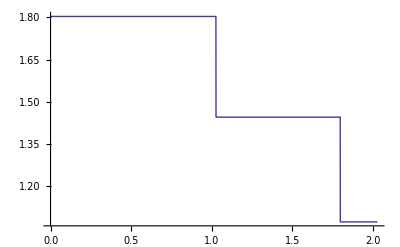
```mathematica
(* Harris and Nielsen model *)
N0YRI = 5125; ts = 55110; N1 = 6900; tmed = 239060; N2 = 8606; tanc = 483890; N3 = 4772;

Pop = Which[t≤0,1,0<t≤(tanc-tmed)/25/(2*N3),N2/N3,(tanc-tmed)/25/(2*N3)<t≤(tanc-ts)/25/(2*N3), N1/N3, (tanc-ts)/25/(2*N3)<t≤ tanc/25/(2*N3),N0YRI/N3];
Plot[Pop,{t,0,tanc/25/(2*N3)}]
-Graphics-
kelleysol = NDSolve[{D[g[x,t],t] == -γ*x*(1-x)*D[g[x,t],x]+1/(2*ρ)*x*(1-x)*D[g[x,t],{x,2}],g[x,0]==θ*(1-x),g[0,t]==θ*ρ,g[1,t]==0}/.{γ->0,θ->1,ρ->Pop},g,{x,0,1},{t,0,tanc/25/(2*N3)}]
{{g->InterpolatingFunction[{{0.,1.},{0.,2.028038558256496}},"<>"]}}
Animate[Plot[Evaluate[g[x,t]/x/.kelleysol],{x,0,1},PlotRange->{{0,1},{0,25}}],{t,0,tanc/25/(2*N3)}]






(* Tennessen et al. model *)
```

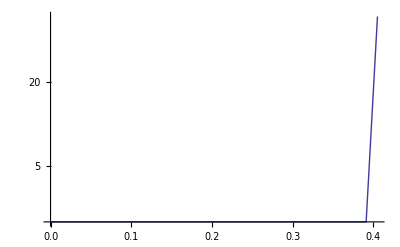
```mathematica
N0ten = 7310;t1ten = 5920;  N1ten  = 14474; t2ten = 205; rten = .0166;


popten = Which[t≤0,1,0≤t≤(t1ten-t2ten)/(2*N0ten),N1ten/N0ten,(t1ten-t2ten)/(2*N0ten)<t≤t1ten/(2*N0ten),N1ten/N0ten*Exp[2*N0ten*rten*(t-(t1ten-t2ten)/(2*N0ten))]];

LogPlot[popten,{t,0,t1ten/(2*N0ten)},PlotRange->All]

-Graphics-
tensol = NDSolve[{D[g[x,t],t] == -γ*x*(1-x)*D[g[x,t],x]+1/(2*ρ)*x*(1-x)*D[g[x,t],{x,2}],g[x,0]==θ*(1-x),g[0,t]==θ*ρ,g[1,t]==0}/.{γ->0,θ->1,ρ->popten},g,{x,0,1},{t,0,t1ten/(2*N0ten)},MaxStepSize->.00025]
{{g->InterpolatingFunction[{{0.,1.},{0.,0.4049247606019152}},"<>"]}}
```